Scattering from the left

```mathematica
psi1[x_] := Exp[I Sqrt[En] x] + RR Exp[-I Sqrt[En] x]
psi2[x_] := AA Exp[I Sqrt[En - V0] x] + BB Exp[-I Sqrt[En - V0] x]
psi3[x_] := TT Exp[I Sqrt[En] x]
```

```mathematica
Solve[{
psi1[-aa] == psi2[-aa],
psi1'[-aa] == psi2'[-aa],
psi2[aa] == psi3[aa],
psi2'[aa] == psi3'[aa]}, {RR, AA, BB, TT}]
```

{{RR→-(-(ⅇ^(-ⅈ aa √(En-V0)) (ⅈ ⅇ^(ⅈ aa √En-ⅈ aa √(En-V0)) √En+ⅈ ⅇ^(ⅈ aa √En-ⅈ aa √(En-V0)) √(En-V0))-ⅇ^(ⅈ aa √(En-V0)) (ⅈ ⅇ^(ⅈ aa √En+ⅈ aa √(En-V0)) √En-ⅈ ⅇ^(ⅈ aa √En+ⅈ aa √(En-V0)) √(En-V0))) (-ⅈ ⅇ^(-ⅈ aa √En+ⅈ aa √(En-V0)) √En-ⅈ ⅇ^(-ⅈ aa √En+ⅈ aa √(En-V0)) √(En-V0))-2 ⅈ ⅇ^(-ⅈ aa √En) (ⅈ ⅇ^(ⅈ aa √En-ⅈ aa √(En-V0)) √En+ⅈ ⅇ^(ⅈ aa √En-ⅈ aa √(En-V0)) √(En-V0)) √(En-V0))/(2 ⅇ^(2 ⅈ aa √En-ⅈ aa √(En-V0)) En-2 ⅇ^(2 ⅈ aa √En+3 ⅈ aa √(En-V0)) En+2 ⅇ^(2 ⅈ aa √En-ⅈ aa √(En-V0)) √En √(En-V0)+2 ⅇ^(2 ⅈ aa √En+3 ⅈ aa √(En-V0)) √En √(En-V0)-ⅇ^(2 ⅈ aa √En-ⅈ aa √(En-V0)) V0+ⅇ^(2 ⅈ aa √En+3 ⅈ aa √(En-V0)) V0),AA→-(2 ⅇ^(-ⅈ aa √En+ⅈ aa √(En-V0)) √En (√En+√(En-V0)))/(-2 En+2 ⅇ^(4 ⅈ aa √(En-V0)) En-2 √En √(En-V0)-2 ⅇ^(4 ⅈ aa √(En-V0)) √En √(En-V0)+V0-ⅇ^(4 ⅈ aa √(En-V0)) V0),BB→-(2 ⅇ^(-ⅈ aa √En+3 ⅈ aa √(En-V0)) √En (-En+√En √(En-V0)+V0))/(√(En-V0) (2 En-2 ⅇ^(4 ⅈ aa √(En-V0)) En+2 √En √(En-V0)+2 ⅇ^(4 ⅈ aa √(En-V0)) √En √(En-V0)-V0+ⅇ^(4 ⅈ aa √(En-V0)) V0)),TT→(4 ⅇ^(-2 ⅈ aa √En+2 ⅈ aa √(En-V0)) √En √(En-V0))/(2 En-2 ⅇ^(4 ⅈ aa √(En-V0)) En+2 √En √(En-V0)+2 ⅇ^(4 ⅈ aa √(En-V0)) √En √(En-V0)-V0+ⅇ^(4 ⅈ aa √(En-V0)) V0)}}

```mathematica
TT := (4 ⅇ^(-2 ⅈ aa √En+2 ⅈ aa √(En-V0)) √En √(En-V0))/(2 En-2 ⅇ^(4 ⅈ aa √(En-V0)) En+2 √En √(En-V0)+2 ⅇ^(4 ⅈ aa √(En-V0)) √En √(En-V0)-V0+ⅇ^(4 ⅈ aa √(En-V0)) V0)
```

```mathematica
FullSimplify[TT]
```

(2 ⅇ^(2 ⅈ (√(-50+En)-√En)) √(-50+En) √En)/(-25+ⅇ^(4 ⅈ √(-50+En)) (25+√(-50+En) √En-En)+√(-50+En) √En+En)

```mathematica
aa := 1
```

```mathematica
V0 := 50
```

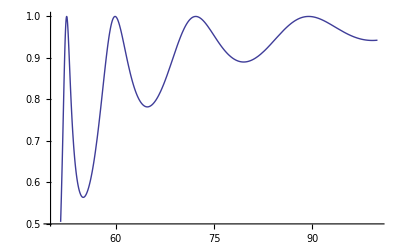

```mathematica
Plot[Norm[TT], {En, V0, 100.0}]
```